```mathematica
I==∫_Subscript[x, 1]^Subscript[x, 2] √(1+f'[x]^2)ⅆx
```

ⅈ==∫_x_1^x_2 √(1+f'[x]^2)ⅆx

```mathematica
L[x,f[x],f'[x]]==∫_Subscript[x, 1]^Subscript[x, 2] √(1+f'[x]^2)ⅆx
```

L[x,f[x],f'[x]]==∫_x_1^x_2 √(1+f'[x]^2)ⅆx

```mathematica
DSolve[L[x,f[x],f'[x]]==∫_Subscript[x, 1]^Subscript[x, 2] √(1+f'[x]^2)ⅆx,{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[L[x,f[x],f'[x]]==∫_x_1^x_2 √(1+f'[x]^2)ⅆx,{f[x]},{x}]

```mathematica
With[{L=Function[x,√(1+f'[x]^2)]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0

```mathematica
DSolve[(f'[x]^2 f''[x])/((1+f'[x]^2)^(3/2))-f''[x]/(√(1+f'[x]^2))==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]+x C[2]}}

```mathematica
With[{L=Function[x,(√(1+f'[x]^2))/f'[x]]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

(f'[x] f''[x])/((1+f'[x]^2)^(3/2))+f''[x]/(f'[x] √(1+f'[x]^2))-(2 √(1+f'[x]^2) f''[x])/f'[x]^3==0

```mathematica
DSolve[%6,{f[x],f[x]},{x}]
```

{{f[x]→-ⅈ √(2/3) x+C[1]},{f[x]→ⅈ √(2/3) x+C[1]},{f[x]→C[1]+x C[2]}}

```mathematica
With[{L=Function[x,1/(√(1+f'[x]^2))]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

-(3 f'[x]^2 f''[x])/((1+f'[x]^2)^(5/2))+f''[x]/((1+f'[x]^2)^(3/2))==0

```mathematica
DSolve[-(3 f'[x]^2 f''[x])/((1+f'[x]^2)^(5/2))+f''[x]/((1+f'[x]^2)^(3/2))==0,{f[x],f[x]},{x}]
```

{{f[x]→-x/(√2)+C[1]},{f[x]→x/(√2)+C[1]},{f[x]→C[1]+x C[2]}}

```mathematica
With[{L=Function[x,f'[x]]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

True

```mathematica
With[{L=Function[x,f'[x] √(1+f'[x]^2)]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

(f'[x]^3 f''[x])/((1+f'[x]^2)^(3/2))-(3 f'[x] f''[x])/(√(1+f'[x]^2))==0

```mathematica
DSolve[(f'[x]^3 f''[x])/((1+f'[x]^2)^(3/2))-(3 f'[x] f''[x])/(√(1+f'[x]^2))==0,{f[x],f[x]},{x}]
```

{{f[x]→C[1]},{f[x]→-ⅈ √(3/2) x+C[1]},{f[x]→ⅈ √(3/2) x+C[1]},{f[x]→C[1]+x C[2]}}

```mathematica
J[{a_,b_}]:={-b,a}
```

```mathematica
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y[t]}]^3
```

(-y'[t] x''[t]+x'[t] y''[t])/((Abs[y[t]]^2+Abs[x'[t]]^2)^(3/2))

```mathematica
FullSimplify[
({x''[t],y''[t]}.J[{x'[t],y'[t]}])/Norm[{x'[t],y[t]}]^3
,{t,x[t],x'[t],y[t],y'[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/((y[t]^2+x'[t]^2)^(3/2))

```mathematica
With[{x=Identity},
(-y'[t] x''[t]+x'[t] y''[t])/((y[t]^2+x'[t]^2)^(3/2))
]
```

y''[t]/((1+y[t]^2)^(3/2))

```mathematica
f''[x]/((1+f[x]^2)^(3/2))
```

f''[x]/((1+f[x]^2)^(3/2))

```mathematica
With[{L=Function[x,f''[x]/((1+f[x]^2)^(3/2))]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

-(3 f[x] f''[x])/((1+f[x]^2)^(5/2))==0

```mathematica
DSolve[-(3 f[x] f''[x])/((1+f[x]^2)^(5/2))==0,{f[x]},{x}]
```

{{f[x]→0},{f[x]→C[1]+x C[2]}}

```mathematica
Power[f''[x]/((1+f[x]^2)^(3/2)),-1]
```

((1+f[x]^2)^(3/2))/f''[x]

```mathematica
With[{L=Function[x,((1+f[x]^2)^(3/2))/f''[x]]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

(3 f[x] √(1+f[x]^2))/f''[x]==0

```mathematica
DSolve[(3 f[x] √(1+f[x]^2))/f''[x]==0,{f[x]},{x}]
```

{{f[x]→0},{f[x]→-ⅈ},{f[x]→ⅈ}}

```mathematica
With[{L=Function[x,f''[x]]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

True

```mathematica
With[{L=Function[x,f[x]]},
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0
]
```

False

```mathematica
(1-a)p+a q
```

(1-a) p+a q

```mathematica
SurfaceData["Sphere", "ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1]
```

Function[{u$,v$},1 {Cos[u$] Sin[v$],Sin[u$] Sin[v$],Cos[v$]}]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1][u,v]
```

{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}

```mathematica
(1-a) p+a q/.{p->{u,v,0},q->{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]},
{u,0,2π},{v,0,2π},PlotRange->{-1,1}],
{a,0,1}]
```

```mathematica
D[{x[t],y[t],z[t]},t]
```

{x'[t],y'[t],z'[t]}

```mathematica
Total@D[{x[t],y[t],z[t]},t]
```

x'[t]+y'[t]+z'[t]

```mathematica
Total@D[{x[t],y[t],z[t]},{t,2}]
```

x''[t]+y''[t]+z''[t]

```mathematica
Normalize[(1-a) p+a q]
```

Normalize[(1-a) p+a q]

```mathematica
Normalize[(1-a) p+a q].Normalize[p]
```

Normalize[(1-a) p+a q].Normalize[p]

```mathematica
FullSimplify[Normalize[(1-a) p+a q].Normalize[p],a∈Reals∧0≤a≤1∧{p,q}∈Reals^2]
```

Normalize[p-a p+a q].Normalize[p]

```mathematica
FullSimplify[
Normalize[(1-a) p+a q].Normalize[p] /.{p->{x[t],y[t]},q->{f[t],g[t]}},
a∈Reals∧0≤a≤1∧{p,q}∈Reals^2]
```

(a f[t] x[t]-(-1+a) x[t]^2+y[t] (a g[t]+y[t]-a y[t]))/(√((Abs[x[t]]^2+Abs[y[t]]^2) (Abs[a f[t]+x[t]-a x[t]]^2+Abs[a g[t]+y[t]-a y[t]]^2)))

```mathematica
FullSimplify[
Normalize[(1-a) p+a q].Normalize[p] /.{p->{x[t],y[t]},q->{f[t],g[t]}},
{t,a,x[t],y[t],f[t],g[t]}∈Reals∧0≤a≤1]
```

(a f[t] x[t]-(-1+a) x[t]^2+y[t] (a g[t]+y[t]-a y[t]))/(√((x[t]^2+y[t]^2) ((a f[t]+x[t]-a x[t])^2+(a g[t]+y[t]-a y[t])^2)))

```mathematica
With[{x=Identity,y=Identity,f=Identity,g=Sin},
(a f[t] x[t]-(-1+a) x[t]^2+y[t] (a g[t]+y[t]-a y[t]))/(√((x[t]^2+y[t]^2) ((a f[t]+x[t]-a x[t])^2+(a g[t]+y[t]-a y[t])^2)))]
```

(-(-1+a) t^2+a t^2+t (t-a t+a Sin[t]))/(√2 √(t^2 (t^2+(t-a t+a Sin[t])^2)))

```mathematica
With[{x=Identity,y=Identity,f=Identity,g=Identity},
(a f[t] x[t]-(-1+a) x[t]^2+y[t] (a g[t]+y[t]-a y[t]))/(√((x[t]^2+y[t]^2) ((a f[t]+x[t]-a x[t])^2+(a g[t]+y[t]-a y[t])^2)))]
```

(t^2-(-1+a) t^2+a t^2)/(2 √(t^4))

```mathematica
With[{x=Identity,y=Identity,f=Identity,g=Identity},
FullSimplify[
(a f[t] x[t]-(-1+a) x[t]^2+y[t] (a g[t]+y[t]-a y[t]))/(√((x[t]^2+y[t]^2) ((a f[t]+x[t]-a x[t])^2+(a g[t]+y[t]-a y[t])^2))),
{a,t}∈Reals∧0≤a≤1]
]
```

1

```mathematica
With[{x=Identity,y=Identity,f=Identity,g=Sin},
FullSimplify[
(a f[t] x[t]-(-1+a) x[t]^2+y[t] (a g[t]+y[t]-a y[t]))/(√((x[t]^2+y[t]^2) ((a f[t]+x[t]-a x[t])^2+(a g[t]+y[t]-a y[t])^2))),
{a,t}∈Reals∧0≤a≤1]
]
```

(t (-(-2+a) t+a Sin[t]))/(√2 √(t^2 (t^2+(t-a t+a Sin[t])^2)))

```mathematica
With[{x=Identity,y=Identity,f=Identity,g=Function[x,x^2]},
FullSimplify[
(a f[t] x[t]-(-1+a) x[t]^2+y[t] (a g[t]+y[t]-a y[t]))/(√((x[t]^2+y[t]^2) ((a f[t]+x[t]-a x[t])^2+(a g[t]+y[t]-a y[t])^2))),
{a,t}∈Reals∧0≤a≤1]
]
```

((2+a (-1+t)) Abs[t])/(√2 √(t^2+(t+a (-1+t) t)^2))

```mathematica
Manipulate[Plot[((2+a (-1+t)) Abs[t])/(√2 √(t^2+(t+a (-1+t) t)^2)),{t,-1.268989575298752,1.268989575298752}],{a,0,1}]
```

```mathematica
Plot3D[
((2+a (-1+t)) Abs[t])/(√2 √(t^2+(t+a (-1+t) t)^2)),
{t,-2,2},{a,0,1}]
```

-Graphics3D-

```mathematica
(1-a) p+a q/.{p->{u,v,0},q->{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
SurfaceData["TorisphericalDome","Properties"]
```

{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]}

{algebraic degree,algebraic equation,alternate names,area element,associated people,Cartesian equation,centroid of solid,Christoffel symbol of the second kind,(map) chromatic number,classes,cross sections,entity classes,Euler characteristic,filled region,coefficients of the first fundamental form,Gaussian curvature,generalized diameter,genus,3-D graphics,image,implicit Gaussian curvature,implicit mean curvature,implicit normal vector,moment of inertia tensor of solid,CDF of lengths,mean line segment length,PDF of lengths,mean curvature,metric tensor,name,number of nodes,normal vector,parameters,parametric equations,principal curvatures,number of punctures,related Wolfram Language symbols,Ricci tensor,Riemann tensor,coefficients of the second fundamental form,semialgebraic description,singular points,sport objects,surface area,variable constraints,variable descriptions,variables,vector length,volume of solid}

```mathematica
SurfaceData["TorisphericalDome",EntityProperty["Surface","Graphics3D"]]
```

-Graphics3D-

```mathematica
SurfaceData["TorisphericalDome",EntityProperty["Surface","Image"]]
```

-Graphics-

```mathematica
SurfaceData["TorisphericalDome",EntityProperty["Surface","GaussianCurvature"]]
```

Missing[NotAvailable]

```mathematica
SurfaceData["TorisphericalDome",EntityProperty["Surface","ParametricEquations"]]
```

Missing[NotAvailable]

```mathematica
SurfaceData["Torus", "ParametricEquations"]
```

Function[{a,c},Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]]

```mathematica
Out[54][1,2]
```

Function[{u$,v$},{(2+1 Cos[v$]) Cos[u$],(2+1 Cos[v$]) Sin[u$],1 Sin[v$]}]

```mathematica
Out[55][u,v]
```

```mathematica
(1-a) p+a q/.{p->{Cos[u] (2+Cos[v]),(2+Cos[v]) Sin[u],Sin[v]},q->{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) Cos[u] (2+Cos[v])+a Cos[u] Sin[v],(1-a) (2+Cos[v]) Sin[u]+a Sin[u] Sin[v],a Cos[v]+(1-a) Sin[v]},
{u,0,2π},{v,0,2π},PlotRange->{-1,1}],
{a,0,1}]
```

```mathematica
Integers
```

ℤ

```mathematica
a+b+c Integers
```

```mathematica
{Complexes,Algebraics,Reals,Rationals,Integers,Primes}
```

{ℂ,Algebraics,ℝ,ℚ,ℤ,Primes}

```mathematica
a+b+c==d ∧a∈Integers∧b∈Reals∧c∈Complexes
```

a+b+c==d&&a∈ℤ&&b∈ℝ&&c∈ℂ

```mathematica
PositiveIntegers
```

```mathematica
a+b+c==d&&a∈&&b∈Reals&&c∈Complexes
```

a+b+c==d&&a∈ℤ&&a>0&&b∈ℝ&&c∈ℂ

```mathematica
PositiveReals
```

```mathematica
a+b+c==d&&a∈Integers&&a>0&&b∈Reals&&c∈Complexes
```

```mathematica
a+b+c==d&&a∈&&b∈&&c∈Complexes
```

a+b+c==d&&a∈ℤ&&a>0&&b∈ℝ&&b>0&&c∈ℂ

```mathematica
Element[Sqrt[2],#]&/@{Complexes,Algebraics,Reals,Rationals,Integers,Primes}
```

{True,True,True,False,False,False}

```mathematica
Hold[TraditionalForm@Element[Sqrt[2],#]&/@{Complexes,Algebraics,Reals,Rationals,Integers,Primes}]
```

Hold[(√2∈#1&)/@{ℂ,Algebraics,ℝ,ℚ,ℤ,Primes}]

```mathematica
(√2∈#1&)/@{Complexes,Algebraics,Reals,Rationals,Integers,Primes}
```

{True,True,True,False,False,False}

```mathematica
Subscript[ℛ, 1]=Disk[{1,1}]
Subscript[ℛ, 2]=Rectangle[{0,0},{1,1}]
Subscript[ℛ, 3]=ImplicitRegion[x^2≤y^3+1,{x,y}]
Subscript[ℛ, 4]=RegionUnion[Disk[{-1,0}],Line[{{0,0},{2,2}}]]
```

Disk[{1,1}]

Rectangle[{0,0},{1,1}]

ImplicitRegion[x^2≤1+y^3,{x,y}]

BooleanRegion[#1||#2&,{Disk[{-1,0}],Line[{{0,0},{2,2}}]}]

```mathematica
Element[{3/2,3/2},#]&/@{Subscript[ℛ, 1],Subscript[ℛ, 2],Subscript[ℛ, 3],Subscript[ℛ, 4]}
```

{True,False,True,True}

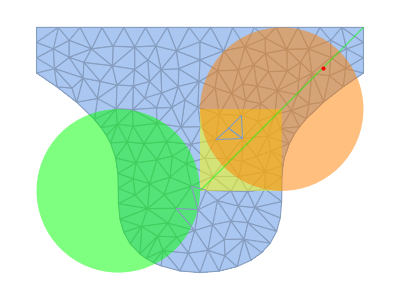

```mathematica
Show[{DiscretizeRegion[Subscript[ℛ, 3]],Graphics[{{Opacity[0.5],{Orange,Subscript[ℛ, 1]},{Yellow,Subscript[ℛ, 2]},{Green,Disk[{-1,0}],Line[{{0,0},{2,2}}]}},{Red,PointSize[Large],Point[{3/2,3/2}]}}]}]
```

```mathematica
GeometricScene[{a,b,c},{Triangle[{a,b,c}],PlanarAngle[{a,b,c}]==30°}]
```

GeometricScene[{{a,b,c},{}},{Triangle[{a,b,c}],PlanarAngle[{a,b,c}]==30 °},{}]

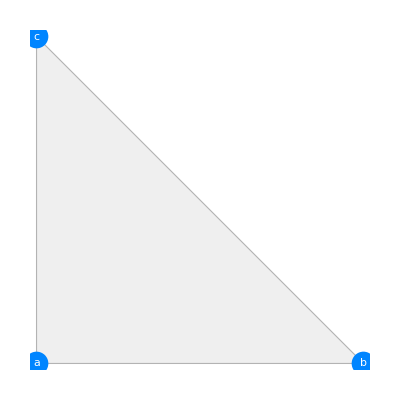

```mathematica
GeometricScene[{a->{0,0},b->{1,0},c->{0,1}},{Triangle[{a,b,c}]}]
```

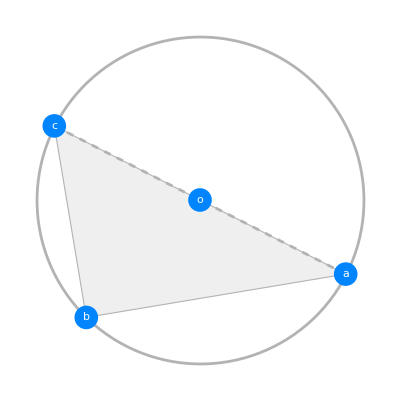

```mathematica
RandomInstance[GeometricScene[{a,b,c,o},{Triangle[{a,b,c}],CircleThrough[{a,b,c},o],o==Midpoint[{a,c}]}]]
```

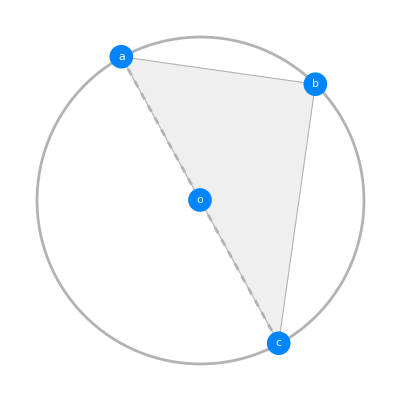

```mathematica
RandomInstance[GeometricScene[{a,b,c,o},{Triangle[{a,b,c}],CircleThrough[{a,b,c},o],o==Midpoint[{a,c}]}]]
```

```mathematica
f[x]
```

f[x]

```mathematica
g[x]
```

g[x]

```mathematica
(1-a)f[x]+a g[x]
```

(1-a) f[x]+a g[x]

```mathematica
∫_0^1 ((1-a) f[x]+a g[x])ⅆa
```

f[x]/2+g[x]/2

```mathematica
∫_a^b √(1+f'[x]^2)ⅆa
```

(-a+b) √(1+f'[x]^2)

```mathematica
∫_a^b √(1+f'[x]^2)ⅆx==∫_a^b √(1+g'[x]^2)ⅆx
```

∫_a^b √(1+f'[x]^2)ⅆx==∫_a^b √(1+g'[x]^2)ⅆx

```mathematica
Reduce[∫_a^b √(1+f'[x]^2)ⅆx==∫_a^b √(1+g'[x]^2)ⅆx]
```

∫_a^b √(1+f'[x]^2)ⅆx==∫_a^b √(1+g'[x]^2)ⅆx

```mathematica
∫_a^b √(1+f'[x]^2)ⅆx==∫_a^b √(1+g'[x]^2)ⅆx
```

```mathematica
D[f[x],x]==√(1+g'[x]^2)
```

f'[x]==√(1+g'[x]^2)

```mathematica
D[g[x],x]==√(1+g'[x]^2)
```

g'[x]==√(1+g'[x]^2)

```mathematica
(g'[x]==√(1+g'[x]^2))^2
```

(g'[x]==√(1+g'[x]^2))^2

```mathematica
(1-a)p+a q
```

(1-a) p+a q

```mathematica
(1-a)p+a q/.{p->{t,t},q->{Cos[t],Sin[t]}}
```

{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},
{t,0,2π}],
{a,0,1}]
```

```mathematica
Manipulate[
Plot[
{(1-a) x+a √(1-x^2),x,√(1-x^2)},
{x,-1,1}],
{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[
{(1-a) t+a t,(1-a) t+a √(1-t^2)},
{t,-2π,2π}],
{a,0,1}]
```

```mathematica
Function[x,x][Function[x,x]]
```

Function[x,x]

```mathematica
Function[x,x][Function[x,x[x]]]
```

Function[x,x[x]]

```mathematica
Function[x,x][Function[x,x[x]]][Function[x,x]]
```

Function[x,x]

```mathematica
a≃b
```

a≃b

```mathematica
{a,b}:A
```

```mathematica
(a(==)_A b)≃(a≃_A b)
```